```mathematica
Monitor[For[Simulation=1,Simulation≤7,Simulation++,
{simi,nsim}={1,20};folder=StringDrop[NotebookDirectory[],-12]<>"data/Sim_";If[Simulation<10,folder=folder<>"0"<>ToString[Simulation]<>"/";,folder=folder<>ToString[Simulation]<>"/";] ;nsim2=nsim-simi+1;pars=0 Range[nsim2];For[i=simi,i≤nsim,i++,run="Run_"<>StringJoin[Table["0",{i,4-IntegerPart[Log[10.,i]]}]];igood=i-simi+1;pars⟦igood⟧=Flatten[Import[folder<>run<>ToString[i]<>"/file_01.dat","Table"]];len=IntegerPart[1/2 Length[pars⟦igood⟧]];Subscript[keep, Simulation,i]=pars[[igood]]]],Row[{ProgressIndicator[i,{1,nsim2}],ToString[i]<>"/"<>ToString[nsim2]}]]
```

```mathematica
pairs=Transpose@{Subscript[keep,1,1][[1;;len]],Subscript[keep,1,1][[len+1;;2 len]]};

cols=7;(*number of pairs per row*)reshapedPairs=Partition[pairs,cols,cols,1,{}];

grr=Grid[Map[Column,reshapedPairs,{2}],(*makes each pair vertical:{a_i,b_i}*)Frame->All,Spacings->{2,1},Alignment->Center,Background->{None,{Lighter[Gray,0.9],White}},ItemStyle->Directive[FontSize->16,FontFamily->"Helvetica"]]
```

t0
0. | tc
-1. | tt
-1. | tmax
100. | Np
200000. | Nc
100. | Nloop
5.
Nreal
1. | Nt
2000. | ntraj
10. | Nci
0. | Nce
100. | Ti
500. | Te
5000.
B0
-1.36875 | vth
218847. | rhoi
0.00166919 | R0
0.921963 | Li
7. | Le
7. | Zeff
2.
Aeff
2. | ndens
1.×10^19 | a0
0.241082 | Omgt0
0. | Omgp0
0. | Omgtprim
0. | wi
1.31109×10^8
C1
133.159 | C2
-50.4644 | C3
1. | safe1
1. | safe2
0. | safe3
5. | amp
1.47429
elong
1.23644 | device
2. | shot
81500. | shotslice
2. | NgridR
150. | NgridZ
150. | Phi
0.
turbprof
20. | Ai
0. | Ae
1. | lambdax
5. | lambday
5. | lambdaz
2. | tauc
50.
k0i
0.1 | k0e
0.1 | X0
1.11718 | Y0
0. | Z0
0. | r00
0.117182 | q00
1.28257
psi0
-0.0133391 | Tw
1. | Ew
1. | pitch
0. | Aw
2. | Zw
1. | taucc
0.
indexmodel
2. | indexlarmor
1. | indexposition
2. | indexpitch
2. | indexenergy
2. | indexcollision
0. | indexturb
1.
indexRMP
0. | indexfrozen
1. | indexpolar
0. | PCC
0. | indexsingle
0. |  |

```mathematica
Export["myMatrixGrid.png",grr,ImageResolution->300]
```

myMatrixGrid.png

```mathematica
Clear["`*"]
e=1.6*10^-19;kB=1.38*10^-23;dens=10^19;temp=10^3*e/kB;pres0=kB dens*temp;μ0=1.25663706212*10^-6;
folder=NotebookDirectory[];
(*"77651";"68408";"81500",""~TCV
"52702","54719","54178";numberfiles={15,6,15}; WEST*)
tokamak="WEST";(*"WEST"*)
If[tokamak=="TCV",{shot2="81500";factorscal=1;np=129;numberfiles=2;}];
If[tokamak=="WEST",{shot2="54178";factorscal=2π;np=201;numberfiles=15;}];
folderdata=StringDrop[folder,-12]<>"G_EQDSK/"<>tokamak<>"/"<>shot2;
SetDirectory[folderdata];
files=FileNames["*.dat"]⟦1;;numberfiles⟧;
data4=Table[Flatten[Import[files⟦i⟧]],{i,Length[files]}];
(*assesing information from imported data*)
{RDIM,ZDIM,RCENTR,RLEFT,ZMID,RMAXIS,ZMAXIS,SIMAG,SIBRY,BCENTR,CURRENT,psi01,a1,a2,a3,a4,a5,a6,a7,a8}=Transpose[data4⟦All,1;;20⟧];
{SIMAG,SIBRY}=factorscal{SIMAG,SIBRY};
```

## Build quantities: grid and on-the-grid

```mathematica
(*R-Z grid*)
δR=Table[RDIM⟦i⟧-0RLEFT[[i]],{i,Length[data4]}]/(np-1);δZ=Table[ZDIM⟦i⟧,{i,Length[data4]}]/(np-1);R2=Table[Table[RLEFT⟦i⟧+δR⟦i⟧ (Range[np]-1),{j,np}]//Transpose,{i,Length[data4]}];
Z2=Table[Table[(2 Range[np]-np-1)/2 δZ⟦i⟧,{j,np}],{i,Length[data4]}];
(*F,P,F',P'*)
FPOL=data4⟦All,20+0 np+1;;20+1 np⟧;
PRES=data4⟦All,20+1 np+1;;20+2 np⟧;
FFPRIM=factorscal data4⟦All,20+2 np+1;;20+3 np⟧;
PPRIME=factorscal data4⟦All,20+3 np+1;;20+4 np⟧;
(*q,ψ,∂_R ψ,∂_Z ψ,∂_RR ψ,∂_RZ ψ,∂_ZZ ψ*)
PSI=factorscal Table[ArrayReshape[data4⟦i,20+4 np+1;;20+(np+4) np⟧,{np,np}]//Transpose,{i,Length[data4]}];
(*plasma boundary*)
{nbbbs,limitr}=data4[[All,20+(np+5)np+1;;20+(np+5)np+2]]//Transpose;
rbound=Table[data4[[as,23+(np+5)np;;22+(np+5)np+2nbbbs[[as]]]],{as,Length[data4]}];
zbound=Table[rbound[[as,2i]],{as,Length[data4]},{i,nbbbs[[as]]}];
rbound=Table[rbound[[as,2i-1]],{as,Length[data4]},{i,nbbbs[[as]]}];
```

```mathematica
Clear["`*"]
```

```mathematica
Simulation=18;
{simi,nsim}={1,999};garbage=0;gcor=0;

folder=StringDrop[NotebookDirectory[],-12]<>"data/Sim_";
If[Simulation<10,folder=folder<>"0"<>ToString[Simulation]<>"/";,folder=folder<>ToString[Simulation]<>"/";]
expfoto=StringTake[folder,StringLength[folder]-15]<>"Arxiv/";
nsim2=nsim-simi+1;
pars=X=Y=Z=q1=q2=q3=Vp=μ=data=H=Q1=Q2=VT=V0=LTT=L0T=LT0=L00=kx=ky=kz=kperp=w=ph=Vcorff=VcorTT=noactparticles=VcorTN=VcorNT=0Range[nsim2];
Monitor[For[i=simi,i≤nsim,i++,
run="Run_"<>StringJoin[Table["0",{i,4-IntegerPart[Log[10.,i]]}]];
igood=i-simi+1;pars⟦igood⟧=Flatten[Import[folder<>run<>ToString[i]<>"/file_01.dat","Table"]];len=IntegerPart[1/2 Length[pars⟦igood⟧]];{names,values}={pars⟦igood,1;;len⟧,pars⟦igood,len+1;;2 len⟧};vars=ToExpression[names];MapThread[Set,{vars,values}];{Nreal,Nc,Np,Nt,Nloop,ntraj}=Rationalize[{Nreal,Nc,Np,Nt,Nloop,ntraj}];
noactparticles[[igood]]=ArrayReshape[BinaryReadList[folder<>run<>ToString[i]<>"/file_24.bin","Real64"],{Nreal,Nloop}];
If[garbage==1,{
X⟦igood⟧=ArrayReshape[BinaryReadList[folder<>run<>ToString[i]<>"/file_02.bin","Real64"],{Nreal,Nloop,ntraj,Nt+1}];Y⟦igood⟧=ArrayReshape[BinaryReadList[folder<>run<>ToString[i]<>"/file_03.bin","Real64"],{Nreal,Nloop,ntraj,Nt+1}];Z⟦igood⟧=ArrayReshape[BinaryReadList[folder<>run<>ToString[i]<>"/file_04.bin","Real64"],{Nreal,Nloop,ntraj,Nt+1}];Vp⟦igood⟧=ArrayReshape[BinaryReadList[folder<>run<>ToString[i]<>"/file_05.bin","Real64"],{Nreal,Nloop,ntraj,Nt+1}];μ⟦igood⟧=ArrayReshape[BinaryReadList[folder<>run<>ToString[i]<>"/file_06.bin","Real64"],{Nreal,Nloop,ntraj,Nt+1}];H⟦igood⟧=ArrayReshape[BinaryReadList[folder<>run<>ToString[i]<>"/file_07.bin","Real64"],{Nreal,Nloop,ntraj,Nt+1}];q1⟦igood⟧=ArrayReshape[BinaryReadList[folder<>run<>ToString[i]<>"/file_08.bin","Real64"],{Nreal,Nloop,ntraj,Nt+1}];q2⟦igood⟧=ArrayReshape[BinaryReadList[folder<>run<>ToString[i]<>"/file_09.bin","Real64"],{Nreal,Nloop,ntraj,Nt+1}];q3⟦igood⟧=ArrayReshape[BinaryReadList[folder<>run<>ToString[i]<>"/file_10.bin","Real64"],{Nreal,Nloop,ntraj,Nt+1}];

kx⟦igood⟧=BinaryReadList[folder<>run<>ToString[i]<>"/file_13.bin","Real64"];ky⟦igood⟧=BinaryReadList[folder<>run<>ToString[i]<>"/file_14.bin","Real64"];kz⟦igood⟧=BinaryReadList[folder<>run<>ToString[i]<>"/file_15.bin","Real64"];kperp⟦igood⟧=BinaryReadList[folder<>run<>ToString[i]<>"/file_16.bin","Real64"];w⟦igood⟧=BinaryReadList[folder<>run<>ToString[i]<>"/file_17.bin","Real64"];ph⟦igood⟧=BinaryReadList[folder<>run<>ToString[i]<>"/file_18.bin","Real64"];
}];
If[gcor==1,Vcorff⟦igood⟧=ArrayReshape[BinaryReadList[folder<>run<>ToString[i]<>"/file_20.bin","Real64"],{Nreal,Nloop,Nt+1,Nt+1}]//Mean//Mean;
VcorTT⟦igood⟧=ArrayReshape[BinaryReadList[folder<>run<>ToString[i]<>"/file_21.bin","Real64"],{Nreal,Nloop,Nt+1,Nt+1}]//Mean//Mean;
VcorTN⟦igood⟧=ArrayReshape[BinaryReadList[folder<>run<>ToString[i]<>"/file_22.bin","Real64"],{Nreal,Nloop,Nt+1,Nt+1}]//Mean//Mean;
VcorNT⟦igood⟧=ArrayReshape[BinaryReadList[folder<>run<>ToString[i]<>"/file_23.bin","Real64"],{Nreal,Nloop,Nt+1,Nt+1}]//Mean//Mean;];
VcorNN=Vcorff-VcorTT-VcorNT-VcorTN;

(*

If[gcor==1,Vcorff⟦igood⟧=ArrayReshape[BinaryReadList[folder<>run<>ToString[i]<>"/file_20.bin","Real64"],{Nreal,Nloop,Nt+1,Nt+1}];
VcorTT⟦igood⟧=ArrayReshape[BinaryReadList[folder<>run<>ToString[i]<>"/file_21.bin","Real64"],{Nreal,Nloop,Nt+1,Nt+1}];
VcorTN⟦igood⟧=ArrayReshape[BinaryReadList[folder<>run<>ToString[i]<>"/file_22.bin","Real64"],{Nreal,Nloop,Nt+1,Nt+1}];
VcorNT⟦igood⟧=ArrayReshape[BinaryReadList[folder<>run<>ToString[i]<>"/file_23.bin","Real64"],{Nreal,Nloop,Nt+1,Nt+1}];];
VcorNN=Vcorff-VcorTT-VcorNT-VcorTN;
*)
dar=ArrayReshape[BinaryReadList[folder<>run<>ToString[i]<>"/file_11.bin","Real64"],{Nreal,Nloop,Nt+1,4}];{Q1⟦igood⟧,VT⟦igood⟧,V0[[igood]],LT0[[igood]]}=Table[dar⟦All,All,All,is⟧,{is,4}];dar=ArrayReshape[BinaryReadList[folder<>run<>ToString[i]<>"/file_12.bin","Real64"],{Nreal,Nloop,Nt+1,4}];{Q2⟦igood⟧,LTT⟦igood⟧,L0T[[igood]],L00[[igood]]}=Table[dar⟦All,All,All,is⟧,{is,4}];
Clear[t0,tc,tt,tmax,Np,Nc,Nloop,Nreal,Nt,ntraj,Nci,Nce,Ti,Te,B0,vth,rhoi,R0,Li,Le,Zeff,Aeff,ndens,a0,Omgt0,Omgp0,Omgtprim,wi,C1,C2,C3,safe1,safe2,safe3,amp,elong,device,shot,shotslice,NgridR,NgridZ,Phi,Ai,turbprof,Ae,lambdax,lambday,lambdaz,tauc,k0i,k0e,X0,Y0,Z0,r00,q00,psi0,Tw,Ew,pitch,Aw,Zw,taucc,indexmodel,indexlarmor,indexposition,indexpitch,indexenergy,indexcollision,indexturb,indexRMP,indexfrozen,indexpolar,PCC,indexsingle];],Row[{ProgressIndicator[i,{1,nsim2}],ToString[i]<>"/"<>ToString[nsim2]}]]
dt=tmax/Nt;ρ=√((X-1.)^2+Y^2);z=Y;x=X Cos[Z];y=X Sin[Z];
Thread[Evaluate[ToExpression[vars]]=Transpose[pars⟦All,1+len;;2 len⟧]];
names2={"t_0","t_c","t_t","t_max","N_p","N_real","N_c","N_loop","N_t","N_traj","N_c_i","N_c_e","T_i [keV]","T_e [keV]","B_0 [T]","v_th [m/s]","ρ_i [m]","R_0 [m]","L_T_i [m^-1]","L_T_e [m^-1]","Z_eff","A_eff","n_0 [10^19m^-3]","a [m]","Ω_t [kHz]","Ω_p [kHz]","Ωp_t","ω_L","C_x","C_y","C_z","q_1","q_2","q_3","Amp","κ","device","#","#time","N_R","N_Z","Φ","turbprof","A_ITG","A_TEM","λ_x [ρ_i]","λ_y [ρ_i]","λ_z [R_0]","τ_c","k_ITG^0","k_TEM^0","X_0","Y_0","Z_0","r_0","q_0","ψ_0","T_s [T_i]","E_s [T_i]","ξ","A_s","Z_S","τ_col","indexmodel","indexlarmor","indexposition","indexpitch","indexenergy","indexcollision","indexturb","indexRMP","indexfrozen","indexpolar","PCC","indexsingle"};
```

```mathematica
aver[dtt_,pas_]:=Table[1/Np[[as]]GaussianFilter[Mean[noactparticles[[as]]dtt⟦as⟧//Mean],pas],{as,nsim2}];speed1[dtt_,τ_]:=Table[Transpose[{τ⟦as⟧,(R0⟦as⟧/vth⟦as⟧)^-1(rhoi[[as]])(RotateLeft[dtt⟦as⟧]-RotateRight[dtt⟦as⟧])/(2τ⟦as,2⟧)}],{as,nsim2}];
difuz1[dtt2_,dtt1_,τ_]:=Table[Transpose[{τ⟦as⟧,(R0⟦as⟧/vth⟦as⟧)^-1(rhoi[[as]])^2(RotateLeft[(dtt2⟦as⟧-dtt1⟦as⟧^2)]-RotateRight[dtt2⟦as⟧-dtt1⟦as⟧^2])/(4τ⟦as,2⟧)}],{as,nsim2}];
speed2[dtt_,τ_]:=Table[Transpose[{τ⟦as⟧,(R0⟦as⟧/vth⟦as⟧)^-1(rhoi[[as]])(dtt⟦as⟧-dtt⟦as,1⟧)/(τ⟦as⟧+10^-9)}],{as,nsim2}];
difuz2[dtt2_,dtt1_,τ_]:=Table[Transpose[{τ⟦as⟧,(R0⟦as⟧/vth⟦as⟧)^-1(rhoi[[as]])^2(dtt2⟦as⟧-dtt1[[as]]^2-(dtt2⟦as,1⟧-dtt1[[as,1]]^2))/(2τ⟦as⟧+10^-9)}],{as,nsim2}];
pas=1;t=Table[dt⟦as⟧(Range[Nt⟦as⟧+1]-1),{as,Length[Q1]}];{𝓆1,𝓆2,π1,π2,𝒽1,𝒽2,𝓋t1,𝓋t2}={aver[Q1,pas],aver[Q2,pas],aver[VT,pas],aver[LTT,pas],aver[V0,pas],aver[L0T,pas],aver[LT0,pas],aver[L00,pas]};
{VQ1,DQ1,VQ2,DQ2,Vπ1,Dπ1,Vπ2,Dπ2,V𝒽1,D𝒽1,V𝒽2,D𝒽2,V𝒯1,D𝒯1,V𝒯2,D𝒯2}={speed1[𝓆1,t],difuz1[𝓆2,𝓆1,t],speed2[𝓆1,t],difuz2[𝓆2,𝓆1,t],speed1[π1,t],difuz1[π2,π1,t],speed2[π1,t],difuz2[π2,π1,t],speed1[𝒽1,t],difuz1[𝒽2,𝒽1,t],speed2[𝒽1,t],difuz2[𝒽2,𝒽1,t],speed1[𝓋t1,t],difuz1[𝓋t2,𝓋t1,t],speed2[𝓋t1,t],difuz2[𝓋t2,𝓋t1,t]};
DQ1[[All,1,2]]=DQ1[[All,2,2]]0;For[i=1,i≤nsim2,i++,DQ1[[i,Nt[[i]]+1,2]]=DQ1[[i,Nt[[i]],2]];];VQ1[[All,1,2]]=VQ1[[All,2,2]];
frac=0.7;frac2=0.95;VQas=Table[VQ1⟦i,IntegerPart[fracNt⟦i⟧];;IntegerPart[Nt⟦i⟧-1],2⟧//Mean,{i,nsim2}];DQas=Table[DQ1⟦i,IntegerPart[fracNt⟦i⟧];;IntegerPart[Nt⟦i⟧-1],2⟧//Mean,{i,nsim2}];
VQas2=Table[VQ2⟦i,IntegerPart[frac2Nt⟦i⟧];;IntegerPart[Nt⟦i⟧-1],2⟧//Mean,{i,nsim2}];DQas2=Table[DQ2⟦i,IntegerPart[frac2Nt⟦i⟧];;IntegerPart[Nt⟦i⟧-1],2⟧//Mean,{i,nsim2}];
varies={"Φ","λ_x","λ_y","λ_z","τ_c","k_0","L_T_e","T_i"};
positions={42,46,47,48,49,51,20,13};
positions={42,46,47,48,49,50,19,13};
```

```mathematica
{ListPlot[VQ1,PlotRange->Automatic],ListPlot[DQ1,PlotRange->Automatic]}
```

```mathematica
{}
```

```mathematica
ψψ=Interpolation[Transpose[{Flatten[R2⟦shotslice[[1]]⟧],Flatten[Z2⟦shotslice[[1]]⟧],Flatten[PSI⟦shotslice[[1]]⟧]}]];
θvals=Range[0,2 Pi,0.05];
eqedge[θ_,r_]:=ψψ[R0⟦1⟧+r Cos[θ],r Sin[θ]]-1.1SIBRY[[1]];
rSoledge[θ_?NumericQ]:=r/.FindRoot[eqedge[θ,r],{r,r00[[1]]}]  (*r0=initial guess for radius*)
rvalsedge=Table[{θ,rSoledge[θ]},{θ,θvals}];
rInterpedge=Interpolation[rvalsedge];
torusedge[θ_,φ_]:={(R0[[1]]+rInterpedge[θ] Cos[θ])Cos[φ],(R0[[1]]+rInterpedge[θ] Cos[θ])Sin[φ],rInterpedge[θ]Sin[θ]};eq[θ_,r_]:=ψψ[R0⟦1⟧+r Cos[θ],r Sin[θ]]-ψψ[R0⟦1⟧+R0⟦1⟧ r00⟦1⟧,0];
rSol[θ_?NumericQ]:=r/.FindRoot[eq[θ,r],{r,r00[[1]]}]  (*r0=initial guess for radius*)
rvals=Table[{θ,rSol[θ]},{θ,θvals}];
rInterp=Interpolation[rvals];
torus[θ_,φ_]:={(R0[[1]]+rInterp[θ] Cos[θ])Cos[φ],(R0[[1]]+rInterp[θ] Cos[θ])Sin[φ],rInterp[θ]Sin[θ]};
Show[ContourPlot[ψψ[a,b],{a,R2[[1]]//Min,R2[[1]]//Max},{b,Z2[[1]]//Min,Z2[[1]]//Max},Contours->23],ParametricPlot[{R0[[1]]+rInterp[θ] Cos[θ],rInterp[θ] Sin[θ]},{θ,0,2 Pi},PlotRange->All]];torusSurface=ParametricPlot3D[{torus[θ,φ],torusedge[θ,φ]},{θ,0,2π},{φ,0,3π/2},Mesh->None,PlotStyle->Directive[Opacity[0.4],ColorFunction->"TemperatureMap",Specularity[White,50]],Lighting->"Neutral",ColorFunctionScaling->True];
```

InterpolatingFunction::dmval: Input value {0.309205,0.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {6.22032,0.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-0.978054,0.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal, but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
whichtraj=5;whichloop=1;Monitor[For[i=1,i≤nsim2,i++,For[j=1,j≤ntraj⟦i⟧,j++,Subscript[trajx, i,j]=Interpolation[Transpose[{t⟦i⟧,R0⟦1⟧ x⟦i,1,whichloop,j⟧}]];Subscript[trajy, i,j]=Interpolation[Transpose[{t⟦i⟧,R0⟦1⟧ y⟦i,1,whichloop,j⟧}]];Subscript[trajz, i,j]=Interpolation[Transpose[{t⟦i⟧,R0⟦1⟧ z⟦i,1,whichloop,j⟧}]];]],{i,j}]
```

```mathematica
limits={{-(1+a0⟦1⟧),1+a0⟦1⟧},{-(1+a0⟦1⟧),1+a0⟦1⟧},{-a0⟦1⟧,a0⟦1⟧}};
{i,j}={5,1};
colors={{Gray},{Red},{Blue},{Green},{Orange},{Pink},{Magenta},{Cyan},{Black},{Brown},{Gray}};
trajs=Table[{Subscript[trajx, i,j][τ],Subscript[trajy, i,j][τ],Subscript[trajz, i,j][τ]},{j,ntraj⟦1⟧}];maxtraject=4;
trajs=Table[ParametricPlot3D[trajs[[ias]],{τ,0, 0.9tmax⟦1⟧},PlotRange->limits,PlotStyle->colors[[ias]]],{ias,2,maxtraject}];
Show[torusSurface,trajs,Boxed->False,Axes->False,ImageSize->Large]
```

```mathematica
whichtraj=6;Monitor[For[i=1,i≤nsim2,i++,For[j=1,j≤ntraj⟦1⟧,j++,Subscript[trajx, i,j]=Interpolation[Transpose[{t⟦i⟧,R0[[i]]X⟦i,1,whichloop,j⟧}]];Subscript[trajy, i,j]=Interpolation[Transpose[{t⟦i⟧,R0[[i]]Y⟦i,1,whichloop,j⟧}]];]],{i,j}]
```

```mathematica
i=11;trajs=Table[{Subscript[trajx, i,j][τ],Subscript[trajy, i,j][τ]},{j,ntraj⟦1⟧}];maxtraject=5;factor =1.7;limits=R0[[i]]{{1-factor a0⟦1⟧,1+factor a0⟦1⟧},{-a0⟦1⟧,a0⟦1⟧}factor };
trajs=Table[ParametricPlot[trajs⟦ias⟧,{τ,0,tmax⟦1⟧/1},PlotRange->limits,PlotStyle->colors[[ias]]],{ias,2,maxtraject}];
```

```mathematica
Show[ParametricPlot[{R0[[1]]+rInterpedge[θ] Cos[θ],rInterpedge[θ] Sin[θ]},{θ,0,2 Pi},PlotRange->limits,PlotStyle->{Black},FrameLabel->{"R [m]","Z [m]"},LabelStyle->{Black,Bold,18},PlotTheme->"Scientific"],trajs,ParametricPlot[{R0[[1]]+rInterp[θ] Cos[θ],rInterp[θ] Sin[θ]},{θ,0,2 Pi},PlotRange->{{0.6,1.4},{-.7,.7}}R0[[i]],PlotStyle->{Green,Dashed}]]
```

```mathematica
i=4;dist=SmoothKernelDistribution[Select[Transpose[{kz⟦i⟧,kperp⟦i⟧} R0⟦i⟧],FreeQ[#1,Indeterminate]&]];
```

```mathematica
Show[DensityPlot[PDF[dist,{x1,y1}]/x1,{x1,0.6 R0⟦i⟧,1.4 R0⟦i⟧},{y1,-.5 R0⟦i⟧,.5 R0⟦i⟧},PlotRange->All,ColorFunction->ColorData["TemperatureMap"],PlotPoints->200,Exclusions->None,Frame->True,FrameLabel->{"R","Z"},LabelStyle->{Black,Bold,18},ImageSize->Large],ParametricPlot[{R0⟦1⟧+rInterp[θ] Cos[θ],rInterp[θ] Sin[θ]},{θ,0,2 π},PlotRange->{{0.6,1.4},{-.5,.5}} R0⟦i⟧,PlotStyle->Orange],ParametricPlot[{R0⟦1⟧+rInterpedge[θ] Cos[θ],rInterpedge[θ] Sin[θ]},{θ,0,2 π},PlotRange->{{0.6,1.4},{-.4,.4}} R0⟦i⟧,PlotStyle->Black]]
```

```mathematica
{size1,size2}={15,18};legend=Grid[{{Graphics[{Red,Rectangle[{0,0}]},ImageSize->size1],Style["D_d^(turb)",size2,FontFamily->"Times New Roman"]},{Graphics[{Blue,Rectangle[{0,0}]},ImageSize->size1],Style["D_L^(turb)",size2,FontFamily->"Times New Roman"]},{Graphics[{Green,Rectangle[{0,0}]},ImageSize->size1],Style["D_L^(turb)",size2,FontFamily->"Times New Roman"]}}];
legend[[1,All,2]]=Table[Style["Φ = "<>ToString[100Phi[[i]]]<>"%",size2,FontFamily->"Times New Roman"],{i,3,10,3}];Histogram[Table[Select[ph⟦i⟧,FreeQ[#1,Indeterminate]&],{i,3,10,3}],{5},PlotRange->{{0,((a0 R0)/rhoi)[[1]]},All},PlotTheme->"Scientific",FrameLabel->{"x","P[x]"},LabelStyle->{Black,Bold,18,FontFamily->"Times New Roman"},ImageSize->Large,ChartStyle->{Red,Blue,Green},ChartLegends->Placed[legend,{{0.8,0.8}}]]
```

```mathematica
ListLinePlot[Table[Select[DQ1⟦i⟧,2.4>#[[2]]>-0.5&],{i,3,10,3}],PlotRange->{All,{-0.5,2.5}},ImageSize->Large,PlotTheme->"Scientific",FrameLabel->{"t[R_0/v_th]","D_r[m^2/s]"},LabelStyle->{Black,Bold,18,FontFamily->"Times New Roman"},PlotStyle->{Red,Blue,Green},PlotLegends->Placed[legend,{{0.8,0.8}}]]
```

```mathematica
ListLinePlot[Table[Select[VQ1⟦i⟧,121.4>#[[2]]>-6.5&],{i,3,10,3}],PlotRange->{All,10{-0.5,4}},ImageSize->Large,PlotTheme->"Scientific",FrameLabel->{"t[R_0/v_th]","V_r[m/s]"},LabelStyle->{Black,Bold,18,FontFamily->"Times New Roman"},PlotStyle->{Red,Blue,Green},PlotLegends->Placed[legend,{{0.8,0.8}}]]
```

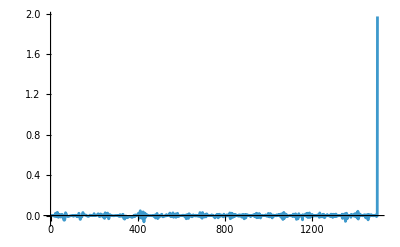
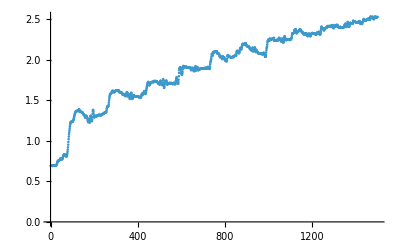

```mathematica
ia=13;{ListLinePlot[Table[H⟦ia,1,1,j⟧-RotateLeft[H⟦ia,1,1,j⟧],{j,7,7+0ntraj⟦1⟧}],PlotRange->All],H[[ia,1,1,4]]//ListPlot}
```

```mathematica
{Phi,lambday,DQas}//Transpose//ListPointPlot3D
```

```mathematica
(*ALL-3D*)
```

```mathematica
initscal=100Phi;
MDI=DQas/initscal;profile=Transpose[Join[Transpose[pars⟦All,positions⟦{1,2,3}⟧+len⟧],{MDI}]];
scaledprof=Transpose[Join[Table[(2. profile⟦All,i⟧)/(Max[profile⟦All,i⟧]-Min[profile⟦All,i⟧])-(Max[profile⟦All,i⟧]+Min[profile⟦All,i⟧])/(Max[profile⟦All,i⟧]-Min[profile⟦All,i⟧]),{i,Length[profile[[1]]]-1}],{MDI}]];
vrb=Table[Subscript[χ, o],{o,Length[profile[[1]]]-1}];model=(α0+∑_i^Length[vrb] Subscript[α1, i] vrb⟦i⟧+∑_i^Length[vrb] ∑_j^Length[vrb] Subscript[α2, i,j] vrb⟦i⟧ vrb⟦j⟧+∑_i^Length[vrb] ∑_j^Length[vrb] ∑_k^Length[vrb] Subscript[α3, i,j,k] vrb⟦i⟧ vrb⟦j⟧vrb⟦k⟧)/(1.0+ ∑_i^Length[vrb] Subscript[β1, i] vrb⟦i⟧+∑_i^Length[vrb] ∑_j^Length[vrb] Subscript[β2, i,j] vrb⟦i⟧ vrb⟦j⟧+∑_i^Length[vrb] ∑_j^Length[vrb] ∑_k^Length[vrb] Subscript[β3, i,j,k] vrb⟦i⟧ vrb⟦j⟧vrb⟦k⟧);prms=Join[{α0},Table[Subscript[α1, i],{i,Length[vrb]}],Flatten[Table[Subscript[α2, i,j],{i,Length[vrb]},{j,Length[vrb]}]],Flatten[Table[Subscript[α3, i,j,k],{i,Length[vrb]},{j,Length[vrb]},{k,Length[vrb]}]],Table[Subscript[β1, i],{i,Length[vrb]}],Flatten[Table[Subscript[β2, i,j],{i,Length[vrb]},{j,Length[vrb]}]],Flatten[Table[Subscript[β3, i,j,k],{i,Length[vrb]},{j,Length[vrb]},{k,Length[vrb]}]]];
vlss=RandomReal[{0,0},Length[prms]];
prms=Transpose[{prms,vlss}];
```

```mathematica
nobas=IntegerPart[0.9*Length[DQas]];fit=model/.FindFit[scaledprof[[1;;nobas]],model,prms,vrb,Method->"ConjugateGradient",MaxIterations->5000]//Simplify//FullSimplify;
g[xa_List]=fit/.Table[Subscript[χ, i]->xa⟦i⟧,{i,Length[profile[[1]]]-1}];
```

FindFit::sdprec: Line search unable to find a sufficient decrease in the function value with MachinePrecision digit precision.

Part::partd: Part specification xa⟦1⟧ is longer than depth of object.

Part::partd: Part specification xa⟦2⟧ is longer than depth of object.

Part::partd: Part specification xa⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

```mathematica
basfit=Table[g[scaledprof[[o,1;;Length[profile[[1]]]-1]]],{o,nobas}]initscal[[1;;nobas]];
basreal=MDI[[1;;nobas]]initscal[[1;;nobas]];
validfit=Table[g[scaledprof[[o,1;;Length[profile[[1]]]-1]]],{o,1+nobas,Length[DQas]}]initscal[[1+nobas;;Length[DQas]]];
validreal=MDI[[1+nobas;;Length[DQas]]]initscal[[1+nobas;;Length[DQas]]];
```

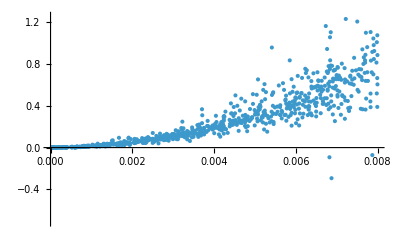

```mathematica
{Phi,MDI}//Transpose//ListPlot
```

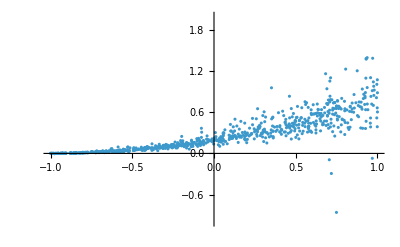
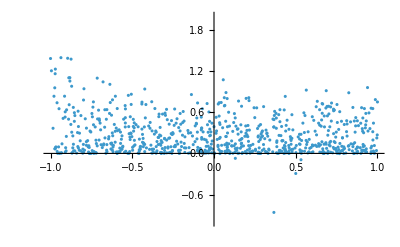
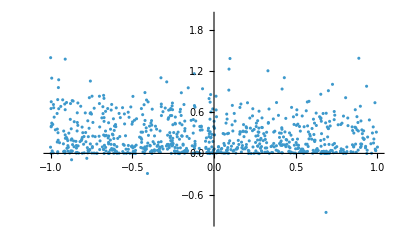

```mathematica
Table[ListPlot[Transpose[{scaledprof⟦All,p⟧,scaledprof[[All,Length[profile[[1]]]]]}],PlotRange->{All,{-1,2}}],{p,Length[profile[[1]]]-1}]
```

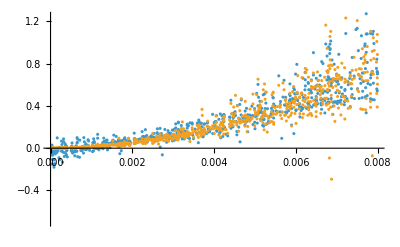
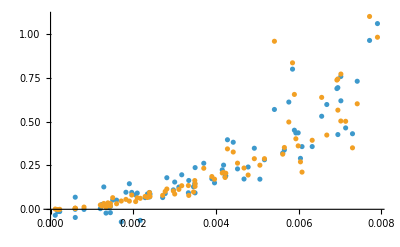

```mathematica
{ListPlot[{{Phi[[1;;nobas]],basfit}//Transpose,{Phi[[1;;nobas]],basreal}//Transpose},PlotRange->Automatic],ListPlot[{{Phi[[1+nobas;;Length[DQas]]],validfit}//Transpose,{Phi[[1+nobas;;Length[DQas]]],validreal}//Transpose},PlotRange->Automatic]}
```

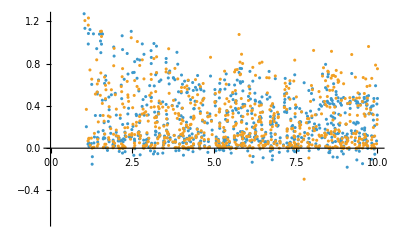
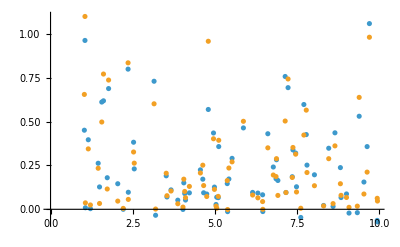

```mathematica
{ListPlot[{{lambdax[[1;;nobas]],basfit}//Transpose,{lambdax[[1;;nobas]],basreal}//Transpose},PlotRange->Automatic],ListPlot[{{lambday[[1+nobas;;Length[DQas]]],validfit}//Transpose,{lambday[[1+nobas;;Length[VQas]]],validreal}//Transpose},PlotRange->Automatic]}
```

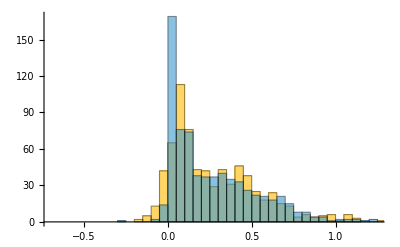
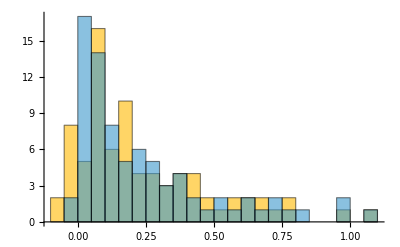

```mathematica
{Histogram[{basfit,basreal},{0.05}],Histogram[{validfit,validreal},{0.05}]}
```

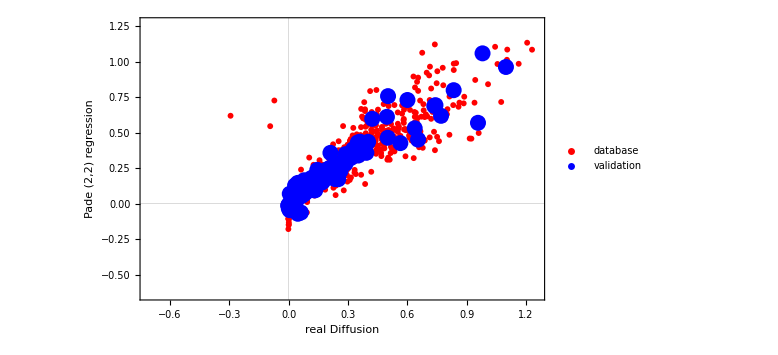

```mathematica
ListPlot[{Transpose[{basreal,basfit}],Transpose[{validreal,validfit}]},PlotStyle->{Red,{Blue,PointSize[0.02]}},PlotTheme->"Scientific",FrameLabel->{"real Diffusion","Pade (2,2) regression"},ImageSize->Large,LabelStyle->{Black,Bold,18,FontFamily->"TimesNewRoman"},PlotLegends->Placed[{"database","validation"},{0.8,0.3}]]
```

```mathematica
(*ALL-2D*)
```

```mathematica
MDI=DQas;profile=Transpose[Join[Transpose[pars⟦All,positions⟦{2,3}⟧+len⟧],{MDI}]];
scaledprof=Transpose[Join[Table[(2. profile⟦All,i⟧)/(Max[profile⟦All,i⟧]-Min[profile⟦All,i⟧])-(Max[profile⟦All,i⟧]+Min[profile⟦All,i⟧])/(Max[profile⟦All,i⟧]-Min[profile⟦All,i⟧]),{i,Length[profile[[1]]]-1}],{MDI}]];
vrb=Table[Subscript[χ, o],{o,Length[profile[[1]]]-1}];model=(α0+∑_i^Length[vrb] Subscript[α1, i] vrb⟦i⟧+∑_i^Length[vrb] ∑_j^Length[vrb] Subscript[α2, i,j] vrb⟦i⟧ vrb⟦j⟧+∑_i^Length[vrb] ∑_j^Length[vrb] ∑_k^Length[vrb] ∑_p^Length[vrb] Subscript[α3, i,j,k,p] vrb⟦i⟧ vrb⟦j⟧vrb⟦k⟧ vrb⟦p⟧)/(1.0+ ∑_i^Length[vrb] Subscript[β1, i] vrb⟦i⟧+∑_i^Length[vrb] ∑_j^Length[vrb] Subscript[β2, i,j] vrb⟦i⟧ vrb⟦j⟧+∑_i^Length[vrb] ∑_j^Length[vrb] ∑_k^Length[vrb] ∑_p^Length[vrb] Subscript[β3, i,j,k,p] vrb⟦i⟧ vrb⟦j⟧vrb⟦k⟧ vrb⟦p⟧);prms=Join[{α0},Table[Subscript[α1, i],{i,Length[vrb]}],Flatten[Table[Subscript[α2, i,j],{i,Length[vrb]},{j,Length[vrb]}]],Flatten[Table[Subscript[α3, i,j,k,p],{i,Length[vrb]},{j,Length[vrb]},{k,Length[vrb]},{p,Length[vrb]}]],Table[Subscript[β1, i],{i,Length[vrb]}],Flatten[Table[Subscript[β2, i,j],{i,Length[vrb]},{j,Length[vrb]}]],Flatten[Table[Subscript[β3, i,j,k,p],{i,Length[vrb]},{j,Length[vrb]},{k,Length[vrb]},{p,Length[vrb]}]]];
vlss=RandomReal[{0,0},Length[prms]];
prms=Transpose[{prms,vlss}];
```

```mathematica
nobas=IntegerPart[0.9*Length[DQas]];fit=model/.FindFit[scaledprof[[1;;nobas]],model,prms,vrb,Method->"LevenbergMarquardt",MaxIterations->2000]//Simplify//FullSimplify;
g[xa_List]=fit/.Table[Subscript[χ, i]->xa⟦i⟧,{i,Length[profile[[1]]]-1}];
basfit=Table[g[scaledprof[[o,1;;Length[profile[[1]]]-1]]],{o,nobas}];
basreal=MDI[[1;;nobas]];
validfit=Table[g[scaledprof[[o,1;;Length[profile[[1]]]-1]]],{o,1+nobas,Length[DQas]}];
validreal=MDI[[1+nobas;;Length[DQas]]];
```

FindFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

Part::partd: Part specification xa⟦1⟧ is longer than depth of object.

Part::partd: Part specification xa⟦2⟧ is longer than depth of object.

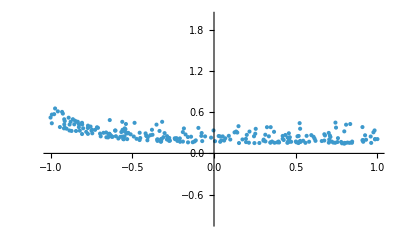
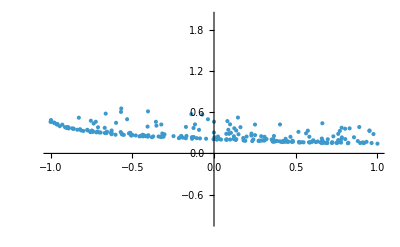

```mathematica
Table[ListPlot[Transpose[{scaledprof⟦All,p⟧,scaledprof[[All,Length[profile[[1]]]]]}],PlotRange->{All,{-1,2}}],{p,Length[profile[[1]]]-1}]
```

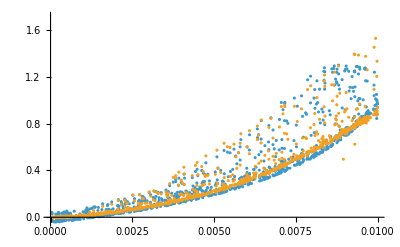
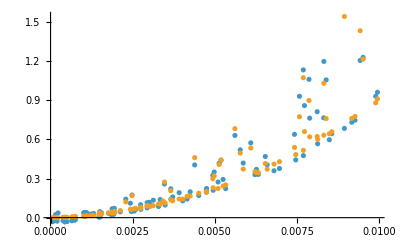

```mathematica
{ListPlot[{{Phi[[1;;nobas]],basfit}//Transpose,{Phi[[1;;nobas]],basreal}//Transpose},PlotRange->Automatic],ListPlot[{{Phi[[1+nobas;;Length[DQas]]],validfit}//Transpose,{Phi[[1+nobas;;Length[DQas]]],validreal}//Transpose},PlotRange->Automatic]}
```

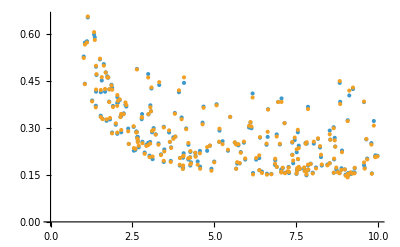
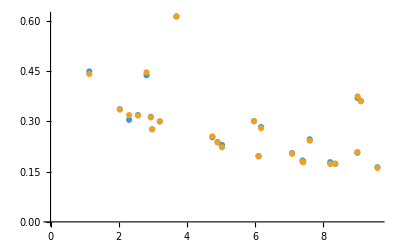

```mathematica
{ListPlot[{{lambdax[[1;;nobas]],basfit}//Transpose,{lambdax[[1;;nobas]],basreal}//Transpose},PlotRange->Automatic],ListPlot[{{lambday[[1+nobas;;Length[DQas]]],validfit}//Transpose,{lambday[[1+nobas;;Length[VQas]]],validreal}//Transpose},PlotRange->Automatic]}
```

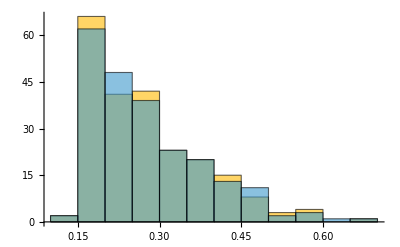
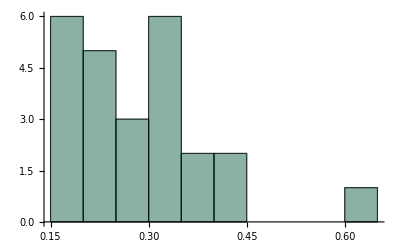

```mathematica
{Histogram[{basfit,basreal},{0.05}],Histogram[{validfit,validreal},{0.05}]}
```

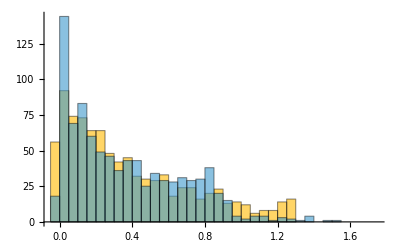
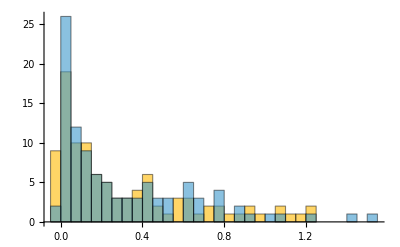

```mathematica
{Histogram[{basfit,basreal},{0.05}],Histogram[{validfit,validreal},{0.05}]}
```

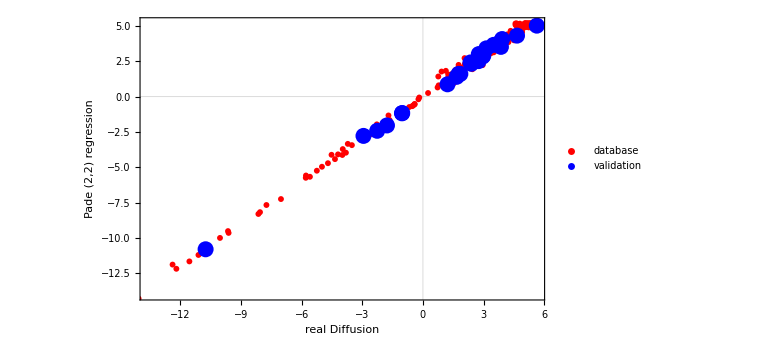

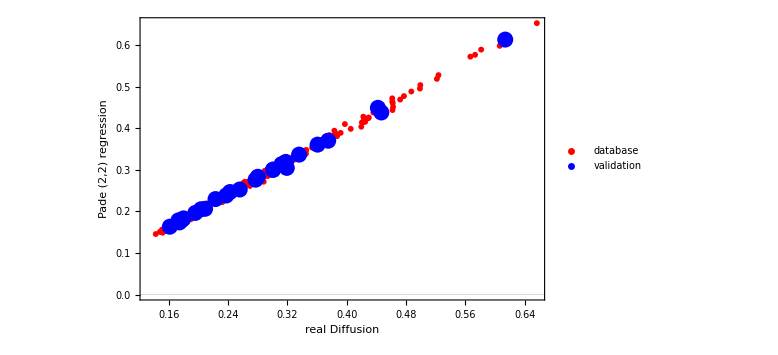

```mathematica
ListPlot[{Transpose[{basreal,basfit}],Transpose[{validreal,validfit}]},PlotStyle->{Red,{Blue,PointSize[0.02]}},PlotTheme->"Scientific",FrameLabel->{"real Diffusion","Pade (2,2) regression"},ImageSize->Large,LabelStyle->{Black,Bold,18,FontFamily->"TimesNewRoman"},PlotLegends->Placed[{"database","validation"},{0.8,0.3}]]
```

```mathematica
fit
```

(0.883766+0.406841 χ_1^2+χ_1 (0.771778-0.0443525 χ_2)+(0.408792-0.0914059 χ_2) χ_2)/(4.30723+1. χ_1^2+(3.636+0.164214 χ_2) χ_2+χ_1 (4.42511+2.57264 χ_2))

```mathematica
ListPlot3D[{{lambdax,lambday,Join[basfit,validfit]}//Transpose,{lambdax,lambday,MDI}//Transpose},PlotRange->All]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

«1 more identical outputs»

```mathematica
(*ALL-5D*)
```

```mathematica
initscal=100Phi;
MDI=VQas/initscal;
MDI=Abs[DQas]/initscal;
profile=Transpose[Join[Transpose[pars⟦All,positions⟦{1,2,3,6,7}⟧+len⟧],{MDI}]];
scaledprof=Transpose[Join[Table[(2. profile⟦All,i⟧)/(Max[profile⟦All,i⟧]-Min[profile⟦All,i⟧])-(Max[profile⟦All,i⟧]+Min[profile⟦All,i⟧])/(Max[profile⟦All,i⟧]-Min[profile⟦All,i⟧]),{i,Length[profile[[1]]]-1}],{MDI}]];
vrb=Table[Subscript[χ, o],{o,Length[profile[[1]]]-1}];model=(α0+∑_i^Length[vrb] Subscript[α1, i] vrb⟦i⟧+∑_i^Length[vrb] ∑_j^Length[vrb] Subscript[α2, i,j] vrb⟦i⟧ vrb⟦j⟧+∑_i^Length[vrb] ∑_j^Length[vrb] ∑_k^Length[vrb] Subscript[α3, i,j,k] vrb⟦i⟧ vrb⟦j⟧vrb⟦k⟧)/(1.0+ ∑_i^Length[vrb] Subscript[β1, i] vrb⟦i⟧+∑_i^Length[vrb] ∑_j^Length[vrb] Subscript[β2, i,j] vrb⟦i⟧ vrb⟦j⟧+∑_i^Length[vrb] ∑_j^Length[vrb] ∑_k^Length[vrb] Subscript[β3, i,j,k] vrb⟦i⟧ vrb⟦j⟧vrb⟦k⟧);prms=Join[{α0},Table[Subscript[α1, i],{i,Length[vrb]}],Flatten[Table[Subscript[α2, i,j],{i,Length[vrb]},{j,Length[vrb]}]],Flatten[Table[Subscript[α3, i,j,k],{i,Length[vrb]},{j,Length[vrb]},{k,Length[vrb]}]],Table[Subscript[β1, i],{i,Length[vrb]}],Flatten[Table[Subscript[β2, i,j],{i,Length[vrb]},{j,Length[vrb]}]],Flatten[Table[Subscript[β3, i,j,k],{i,Length[vrb]},{j,Length[vrb]},{k,Length[vrb]}]]];
vlss=RandomReal[{-0.05,0.05},Length[prms]];
prms=Transpose[{prms,vlss}];
```

```mathematica
nobas=IntegerPart[0.9*Length[DQas]];fit=model/.FindFit[scaledprof[[1;;nobas]],model,prms,vrb,Method->"ConjugateGradient",MaxIterations->5000]//Simplify//FullSimplify;
g[xa_List]=fit/.Table[Subscript[χ, i]->xa⟦i⟧,{i,Length[profile[[1]]]-1}];
```

FindFit::sdprec: Line search unable to find a sufficient decrease in the function value with MachinePrecision digit precision.

Part::partd: Part specification xa⟦1⟧ is longer than depth of object.

Part::partd: Part specification xa⟦2⟧ is longer than depth of object.

Part::partd: Part specification xa⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

```mathematica
basfit=Table[g[scaledprof[[o,1;;Length[profile[[1]]]-1]]],{o,nobas}]initscal[[1;;nobas]];
basreal=MDI[[1;;nobas]]initscal[[1;;nobas]];
validfit=Table[g[scaledprof[[o,1;;Length[profile[[1]]]-1]]],{o,1+nobas,Length[DQas]}]initscal[[1+nobas;;Length[DQas]]];
validreal=MDI[[1+nobas;;Length[DQas]]]initscal[[1+nobas;;Length[DQas]]];
```

```mathematica
cc=100ϕ g[{ϕ,5,5,0.1,12}]//FullSimplify
```

(ϕ (-85194.6+ϕ (-162557.+ϕ (-4455.3+1012.97 ϕ))))/(-1869.07+ϕ (-346.212+ϕ (11.2208+1. ϕ)))

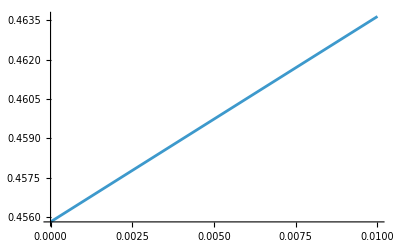

```mathematica
Plot[cc,{ϕ,0,0.01}]
```

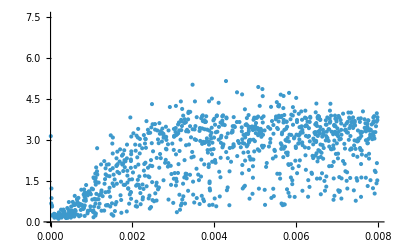

```mathematica
{Phi,MDI}//Transpose//ListPlot
```

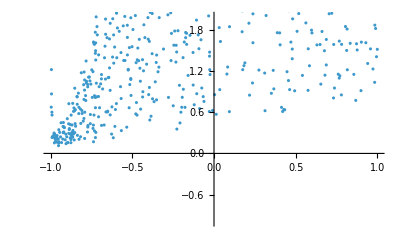
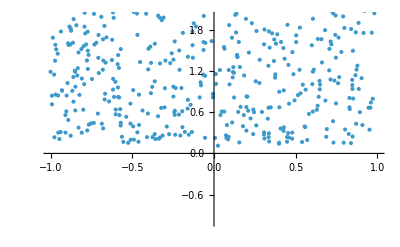
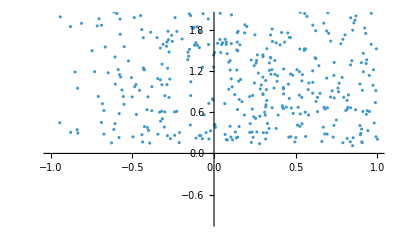
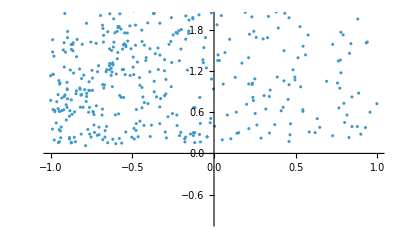
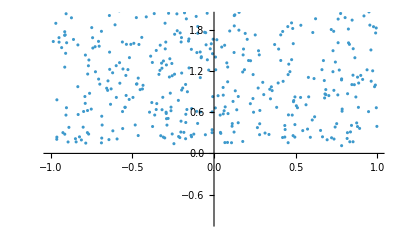

```mathematica
Table[ListPlot[Transpose[{scaledprof⟦All,p⟧,scaledprof[[All,Length[profile[[1]]]]]}],PlotRange->{All,{-1,2}}],{p,Length[profile[[1]]]-1}]
```

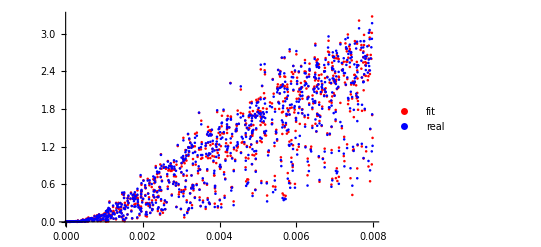
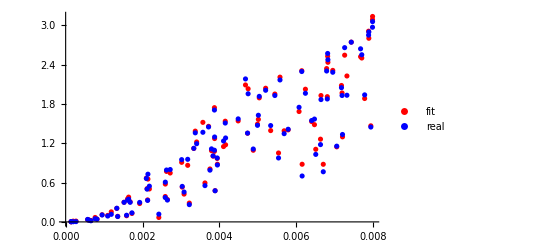

```mathematica
{ListPlot[{{Phi[[1;;nobas]],basfit}//Transpose,{Phi[[1;;nobas]],basreal}//Transpose},PlotRange->Automatic,PlotStyle->{Red,Blue},PlotLegends->{"fit","real"}],ListPlot[{{Phi[[1+nobas;;Length[DQas]]],validfit}//Transpose,{Phi[[1+nobas;;Length[DQas]]],validreal}//Transpose},PlotRange->Automatic,PlotStyle->{Red,Blue},PlotLegends->{"fit","real"}]}
```

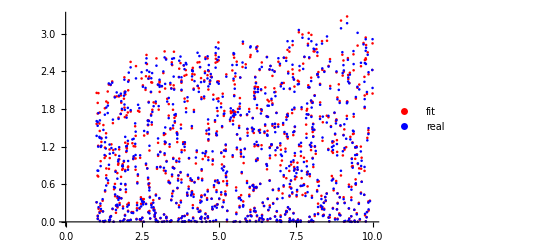
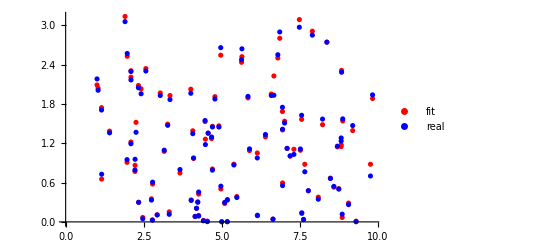

```mathematica
{ListPlot[{{lambdax[[1;;nobas]],basfit}//Transpose,{lambdax[[1;;nobas]],basreal}//Transpose},PlotRange->Automatic,PlotStyle->{Red,Blue},PlotLegends->{"fit","real"}],ListPlot[{{lambday[[1+nobas;;Length[DQas]]],validfit}//Transpose,{lambday[[1+nobas;;Length[VQas]]],validreal}//Transpose},PlotRange->Automatic,
PlotStyle->{Red,Blue},PlotLegends->{"fit","real"}]}
```

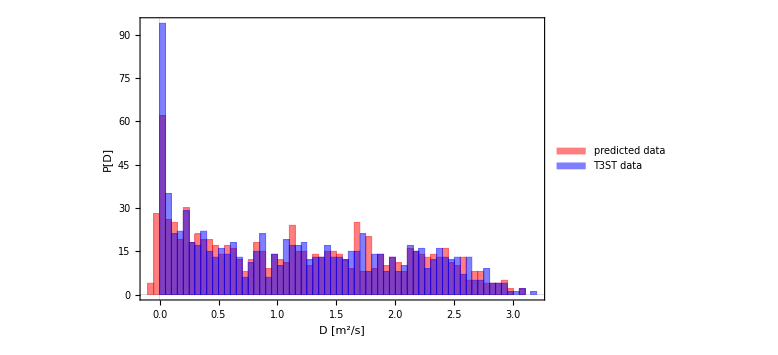
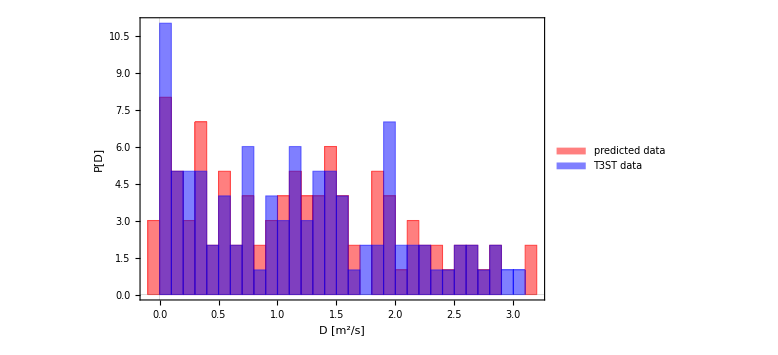

```mathematica
{Histogram[{basfit,basreal},{-0.1,3.2,0.05},ChartStyle->{Red,Blue},ChartLegends->Placed[{Style["predicted data",20],Style["T3ST data",20]},{0.8,0.7}],FrameLabel->{"D [m^2/s]","P[D]"},PlotTheme->"Scientific",ImageSize->Large,LabelStyle->{Black,Bold,18,FontFamily->"TimesNewRoman"}],Histogram[{validfit,validreal},{-0.1,3.2,0.1},ChartStyle->{Red,Blue},ChartLegends->Placed[{Style["predicted data",20],Style["T3ST data",20]},{0.8,0.7}],FrameLabel->{"D [m^2/s]","P[D]"},PlotTheme->"Scientific",ImageSize->Large,LabelStyle->{Black,Bold,18,FontFamily->"TimesNewRoman"}]}
```

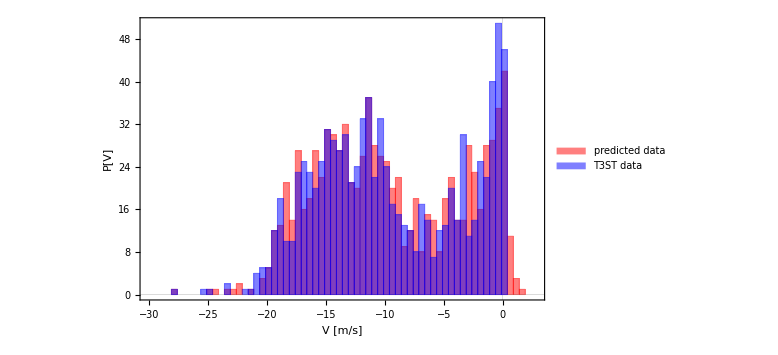
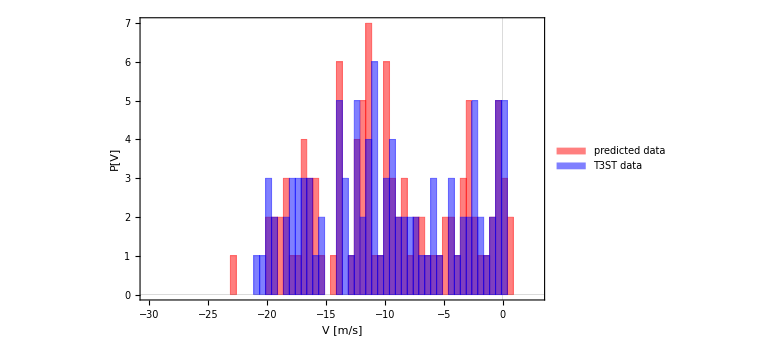

```mathematica
{Histogram[{basfit,basreal},{-30.1,3.2,0.5},ChartStyle->{Red,Blue},ChartLegends->Placed[{Style["predicted data",20],Style["T3ST data",20]},{0.8,0.7}],FrameLabel->{"V [m/s]","P[V]"},PlotTheme->"Scientific",ImageSize->Large,LabelStyle->{Black,Bold,18,FontFamily->"TimesNewRoman"}],Histogram[{validfit,validreal},{-30.1,3.2,0.5},ChartStyle->{Red,Blue},ChartLegends->Placed[{Style["predicted data",20],Style["T3ST data",20]},{0.8,0.7}],FrameLabel->{"V [m/s]","P[V]"},PlotTheme->"Scientific",ImageSize->Large,LabelStyle->{Black,Bold,18,FontFamily->"TimesNewRoman"}]}
```

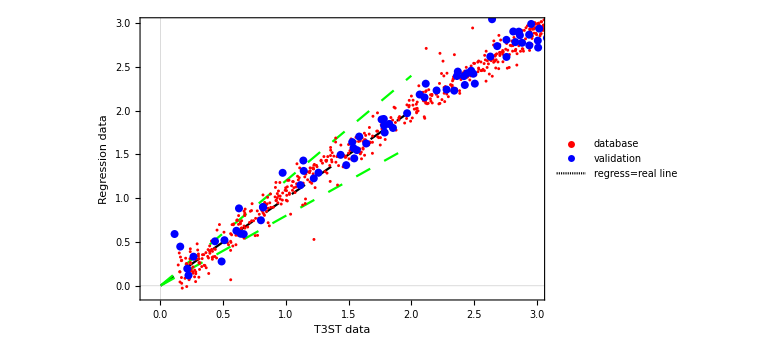
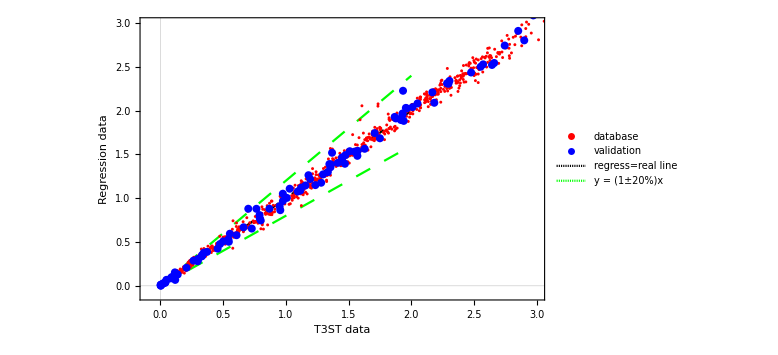

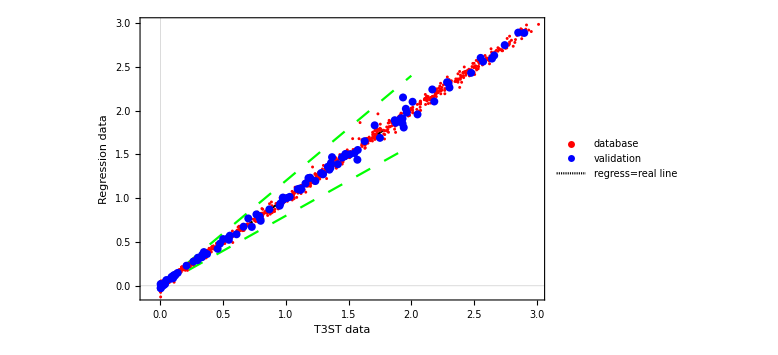
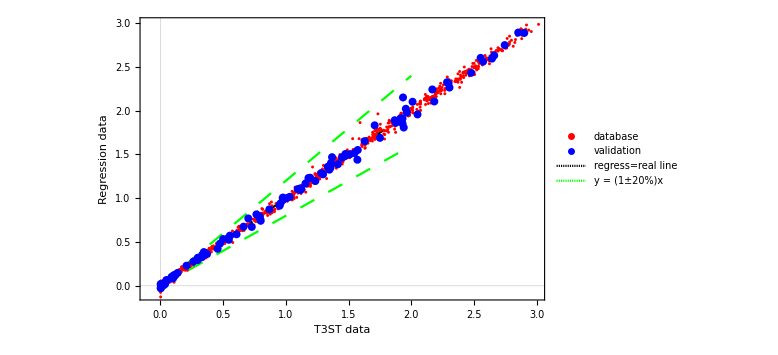

```mathematica
unu=(Range[10^3] 2)/10^3;
unuplus=Transpose[{unu,1.2unu}];unuminus=Transpose[{unu,0.8unu}];unu=Transpose[{unu,unu}];
{ListPlot[{Transpose[{basreal/initscal⟦1;;nobas⟧^1,basfit/initscal⟦1;;nobas⟧^1}],Transpose[{validreal/initscal⟦1+nobas;;Length[initscal]⟧^1,validfit/initscal⟦1+nobas;;Length[initscal]⟧^1}],unu,unuplus,unuminus},PlotStyle->{Red,{Blue,PointSize[0.01]},{Black,Dashing[.02,0]},{Green,Dashing[.02,0]},{Green,Dashing[.02,0]}},PlotRange->{{-0.1,3},{-0.1,3}},Joined->{False,False,True,True,True},PlotTheme->"Scientific",FrameLabel->{"T3ST data","Regression data"},ImageSize->Large,LabelStyle->{Black,Bold,18,FontFamily->"TimesNewRoman"},PlotLegends->Placed[{"database","validation","regress=real line"},{0.8,0.2}]],ListPlot[{Transpose[{basreal/initscal⟦1;;nobas⟧^0,basfit/initscal⟦1;;nobas⟧^0}],Transpose[{validreal/initscal⟦1+nobas;;Length[initscal]⟧^0,validfit/initscal⟦1+nobas;;Length[initscal]⟧^0}],unu,unuplus,unuminus},PlotStyle->{Red,{Blue,PointSize[0.01]},{Black,Dashing[.02,0]},{Green,Dashing[.02,0]},{Green,Dashing[.02,0]}},PlotRange->{{-0.1,3},{-0.1,3}},Joined->{False,False,True,True,True},PlotTheme->"Scientific",FrameLabel->{"T3ST data","Regression data"},
ImageSize->Large,LabelStyle->{Black,Bold,18,FontFamily->"TimesNewRoman"},PlotLegends->Placed[{"database","validation","regress=real line","y = (1±20%)x"},{0.82,0.25}]]}
```

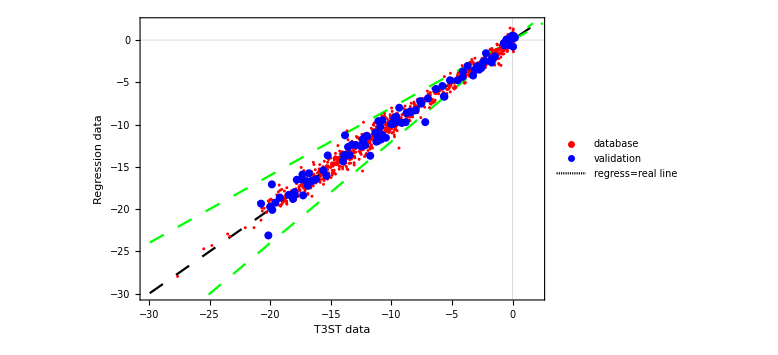
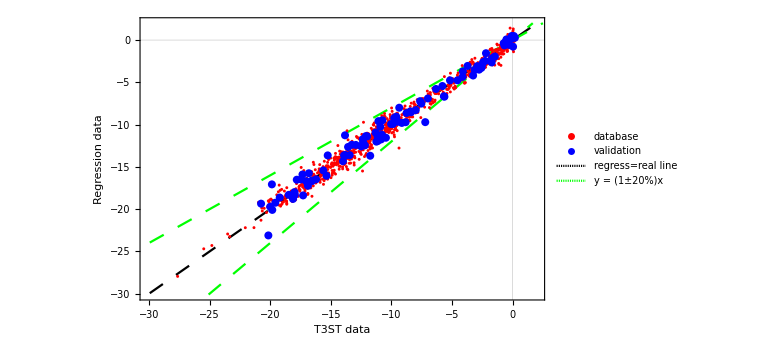

```mathematica
unu=30(-1+(Range[10^3] 2)/10^3);
unuplus=Transpose[{unu,1.2unu}];unuminus=Transpose[{unu,0.8unu}];unu=Transpose[{unu,unu}];
{ListPlot[{Transpose[{basreal/initscal⟦1;;nobas⟧^1,basfit/initscal⟦1;;nobas⟧^1}],Transpose[{validreal/initscal⟦1+nobas;;Length[initscal]⟧^1,validfit/initscal⟦1+nobas;;Length[initscal]⟧^1}],unu,unuplus,unuminus},PlotStyle->{Red,{Blue,PointSize[0.01]},{Black,Dashing[.02,0]},{Green,Dashing[.02,0]},{Green,Dashing[.02,0]}},PlotRange->{{-30.1,2},{-30.1,2}},Joined->{False,False,True,True,True},PlotTheme->"Scientific",FrameLabel->{"T3ST data","Regression data"},ImageSize->Large,LabelStyle->{Black,Bold,18,FontFamily->"TimesNewRoman"},PlotLegends->Placed[{"database","validation","regress=real line"},{0.8,0.2}]],ListPlot[{Transpose[{basreal/initscal⟦1;;nobas⟧^0,basfit/initscal⟦1;;nobas⟧^0}],Transpose[{validreal/initscal⟦1+nobas;;Length[initscal]⟧^0,validfit/initscal⟦1+nobas;;Length[initscal]⟧^0}],unu,unuplus,unuminus},PlotStyle->{Red,{Blue,PointSize[0.01]},{Black,Dashing[.02,0]},{Green,Dashing[.02,0]},{Green,Dashing[.02,0]}},PlotRange->{{-30.1,2},{-30.1,2}},Joined->{False,False,True,True,True},PlotTheme->"Scientific",FrameLabel->{"T3ST data","Regression data"},
ImageSize->Large,LabelStyle->{Black,Bold,18,FontFamily->"TimesNewRoman"},PlotLegends->Placed[{"database","validation","regress=real line","y = (1±20%)x"},{0.82,0.25}]]}
```

```mathematica
(*Φ*)
```

Part::partw: Part 11 of {Φ,λ_x,λ_y,λ_z,τ_c,k_0,L_T_e,T_i} does not exist.

NumberForm::reqsigz: Requested number precision is lower than number of digits shown; padding with zeros.

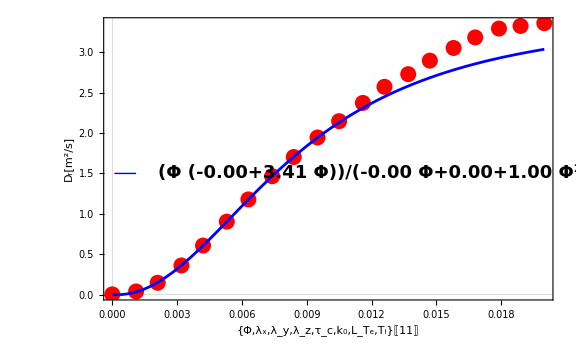
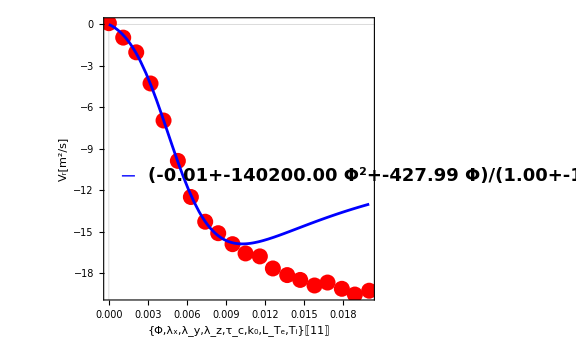

```mathematica
start=10;profile=Transpose[{pars[[All,positions[[Simulation-start]]+len]],DQas}];η=0.99999;model=(A2 χ 10^2+A3 10^4 χ^2)/(1.0+10^2 η A4 χ+A5 10^4 χ^2);variable={A1,A2,A3,A4,A5};fit=model/.FindFit[Drop[profile,-10],model,variable,χ]//Simplify;
{height,width,formula}={1.5,0.0001,fit/.x_Real:>NumberForm[x,{5,2}]/.χ->Φ};g1=Show[ListPlot[profile,PlotTheme->"Scientific",PlotStyle->{Red,PointSize[0.02]},ImageSize->Large,FrameLabel->{varies[[Simulation]]//TraditionalForm,"D_r[m^2/s]"},LabelStyle->{Black,Bold,20,FontFamily->"TimesNewRoman"},Epilog->{Blue,Thick,Line[{{width,height},{width+0.001,height}}],Text[Style[formula,18,Black,Bold,FontFamily->"Times New Roman"],{width+0.002,height},{Left,Center}]}],Plot[fit,{χ,Min[profile[[All,1]]],Max[profile[[All,1]]]},PlotStyle->Blue]];
profile=Transpose[{pars[[All,positions[[Simulation-start]]+len]],VQas}];model=(A1+A2 χ 10^2+A3 10^4 χ^2)/(1.0+10^2 η A4 χ+A5 10^4 χ^2);variable={A1,A2,A3,A4,A5};fit=model/.FindFit[Drop[profile,-10],model,variable,χ]//Simplify;
{height,width,formula}={-10.95,0.001,fit/.x_Real:>NumberForm[x,{5,2}]/.χ->Φ};g2=Show[ListPlot[profile,PlotTheme->"Scientific",PlotStyle->{Red,PointSize[0.02]},ImageSize->Large,FrameLabel->{varies[[Simulation]]//TraditionalForm,"V_r[m^2/s]"},LabelStyle->{Black,Bold,20,FontFamily->"TimesNewRoman"},Epilog->{Blue,Thick,Line[{{width,height},{width+0.001,height}}],Text[Style[formula,18,Black,Bold,FontFamily->"Times New Roman"],{width+0.002,height},{Left,Center}]}],Plot[fit,{χ,Min[profile[[All,1]]],Max[profile[[All,1]]]},PlotStyle->Blue]];
{g1,g2}
```

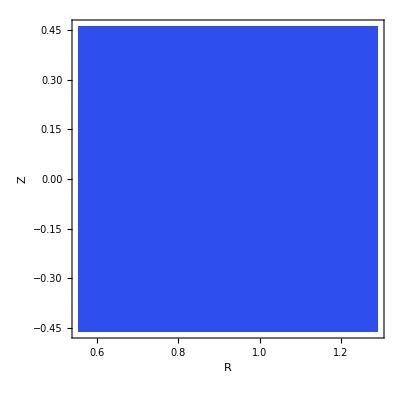
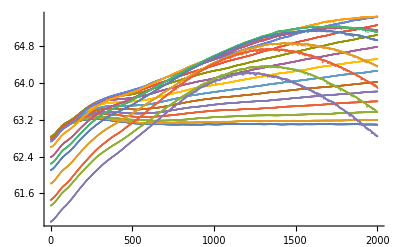
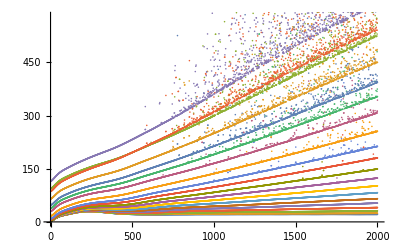
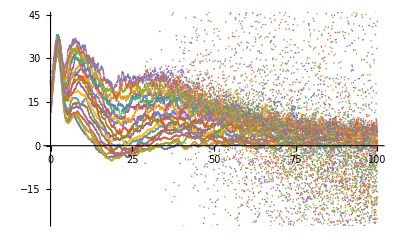
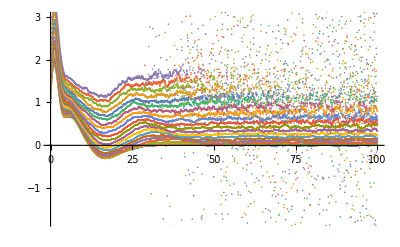

```mathematica
4=19;dist=SmoothKernelDistribution[Select[{kz[[i]],kperp[[i]]}R0[[i]]//Transpose,FreeQ[#,Indeterminate]&]];
{DensityPlot[PDF[dist,{x1,y1}],{x1,0.6R0[[i]],1.4R0[[i]]},{y1,-.5R0[[i]],0.5R0[[i]]},PlotRange->All,ColorFunction->ColorData["TemperatureMap"],PlotPoints->100,Exclusions->None,Frame->True,FrameLabel->{"R","Z"},LabelStyle->{Black,Bold,18}],ListPlot[𝓆1,PlotRange->All],ListPlot[𝓆2-𝓆1^2,PlotRange->Automatic],ListPlot[VQ1,PlotRange->Automatic],ListPlot[DQ1,PlotRange->Automatic]}
```

```mathematica
(*λx*)
```

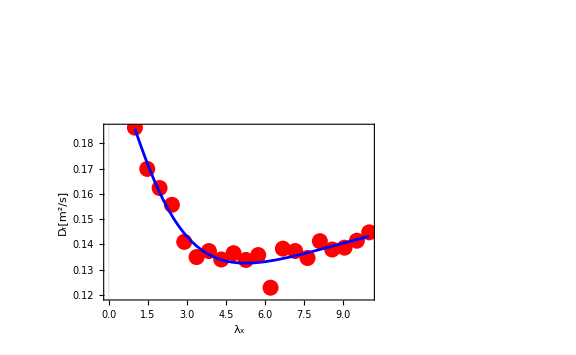
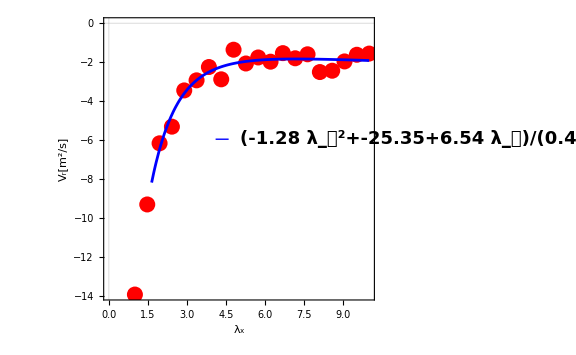

```mathematica
start=10;profile=Transpose[{pars[[All,positions[[Simulation-start]]+len]],DQas}];model=A1+A2/(A3+χ^2)+0(A1(χ)^2)/(A2(χ)^2+χ  A3+A4);η=0.99999;model=(A1+A2 χ+A3 χ^2)/(1.0+0η A4 χ+A5 χ^2);variable={A1,A2,A3,A4,A5};fit=model/.FindFit[profile,model,variable,χ]//Simplify;
{height,width,formula}={0.4,4,fit/.x_Real:>NumberForm[x,{5,2}]/.χ->Subscript[λ, 𝓍]};g1=Show[ListPlot[profile,PlotTheme->"Scientific",PlotStyle->{Red,PointSize[0.02]},ImageSize->Large,FrameLabel->{varies[[Simulation-start]]//TraditionalForm,"D_r[m^2/s]"},LabelStyle->{Black,Bold,20,FontFamily->"TimesNewRoman"},Epilog->{Blue,Thick,Line[{{width,height},{width+0.5,height}}],Text[Style[formula,18,Black,Bold,FontFamily->"Times New Roman"],{width+0.9,height},{Left,Center}]}],Plot[fit,{χ,Min[profile[[All,1]]],Max[profile[[All,1]]]},PlotStyle->Blue,PlotRange->All]];
profile=Transpose[{pars[[All,positions[[Simulation-start]]+len]],VQas}];η=0.99999;model=(A1+A2 χ+A3 χ^2)/(1.0+0η A4 χ+A5 χ^2);variable={A1,A2,A3,A4,A5};fit=model/.FindFit[profile,model,variable,χ]//Simplify;
{height,width,formula}={-5.95,4.1,fit/.x_Real:>NumberForm[x,{5,2}]/.χ->Subscript[λ, 𝓍]};g2=Show[ListPlot[profile,PlotTheme->"Scientific",PlotStyle->{Red,PointSize[0.02]},ImageSize->Large,FrameLabel->{varies[[Simulation-start]]//TraditionalForm,"V_r[m^2/s]"},LabelStyle->{Black,Bold,20,FontFamily->"TimesNewRoman"},Epilog->{Blue,Thick,Line[{{width,height},{width+0.5,height}}],Text[Style[formula,18,Black,Bold,FontFamily->"Times New Roman"],{width+0.92,height},{Left,Center}]}],Plot[fit,{χ,Min[profile[[All,1]]],Max[profile[[All,1]]]},PlotStyle->Blue]];
{g1,g2}
```